```mathematica
En[kBT_]=-J Tanh[J/kBT]
Cv[kBT_] = (J/kBT)^2/Cosh[J/kBT]^(2)
```

-J Tanh[J/kBT]

(J^2 Sech[J/kBT]^2)/kBT^2

```mathematica
Numerator[(J^2 Sech[J/kBT]^2)/kBT^2]
```

J^2 Sech[J/kBT]^2

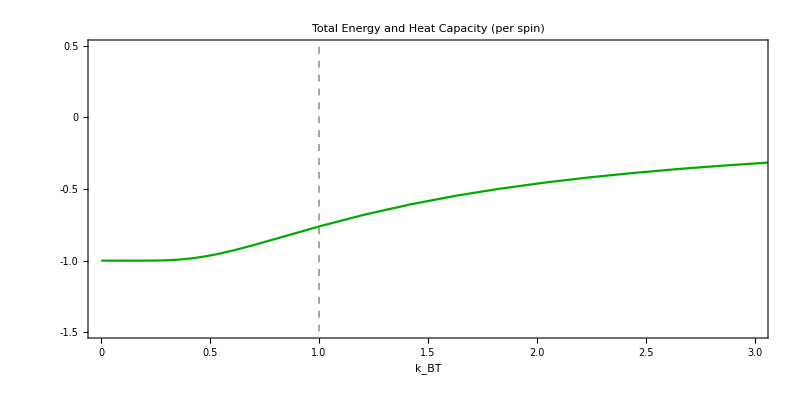

```mathematica
Plot[En[T]/.J->1,{T,0,10},PlotLabel->Style["Total Energy and Heat Capacity (per spin)",Black,28],PlotRange->{{0,3},{-1.5,0.5}},PlotLegends->Placed[{},{0.9,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["k_BT",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Darker[Green]},{Blue}},Epilog->{Gray,Dashed,Line[{{1,-10},{1,5}}]}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p1(1)_image.png",%,ImageResolution->500];
```

General::munfl: Sech[4895.1] is too small to represent as a normalized machine number; precision may be lost.

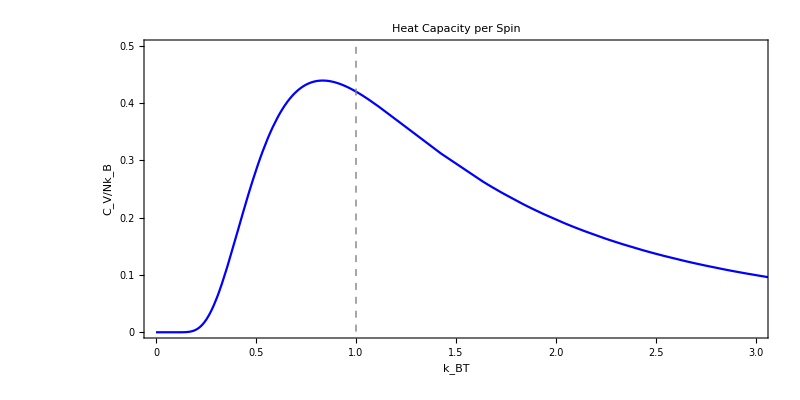

```mathematica
Plot[Cv[T]/.J->1,{T,0,10},PlotLabel->Style["Heat Capacity per Spin",Black,28],PlotRange->{{0,3},{0,0.5}},PlotLegends->Placed[{},{0.9,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["C_V/Nk_B",Black,28],None},{Style["k_BT",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{Blue},Epilog->{Gray,Dashed,Line[{{1,-10},{1,10}}]}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p1(2)_image.png",%,ImageResolution->500];
```

```mathematica
UnitConvert[Quantity[1,"ElementaryCharge"^2/"BohrRadius"/"ElectricConstant"]/(4 Pi),"ElectronVolts"]
```

27.2113862 eV

```mathematica
UnitConvert[Quantity[1,"MagneticConstant""BohrMagneton"^2/"BohrRadius"^3]/(4 Pi),"ElectronVolts"]
```

0.00036226079 eV

```mathematica
N[UnitConvert[Quantity[300,"BoltzmannConstant"*"Kelvins"],"ElectronVolts"]]
```

0.025852 eV

```mathematica
γ[α_,κ_,B_]= FullSimplify[Coth[α Beff]-Coth[α Beff/2]/2/.{Beff->(κ m+B),J0->κ μ^2}]
```

1/2 Tanh[1/2 α (B+m κ)]

```mathematica
γ[α,κ,B]
```

1/2 Tanh[1/2 α (B+m κ)]

```mathematica
Plot[Evaluate[{m,γ[0.25,1,0],γ[0.5,1,0],γ[1,1,0],γ[2,1,0],γ[5,1,0],γ[10,1,0]}],{m,-5,5},PlotLabel->Style["MFT Magnetization at B=0",Black,28],PlotRange->{{-3,3},{-0.75,0.75}},PlotLegends->Placed[{Style["m",20],Style["1/2tanh[ακm/2], ακ=1/4",20],Style["1/2tanh[ακm/2], ακ=1/2",20],Style["1/2tanh[ακm/2], ακ=1",20],Style["1/2tanh[ακm/2], ακ=2",20],Style["1/2tanh[ακm/2], ακ=5",20],Style["1/2tanh[ακm/2], ακ=10",20]},{1.1,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {1100,400},AspectRatio->Full,PlotStyle->{{Black,Dashed},{Pink},{Green},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2c(1)_image.png",%,ImageResolution->500];
```

-Graphics-

```mathematica
Series[Tanh[x],{x,0,4}]
```

x-x^3/3+O[x]^5

```mathematica
B=1;
Plot[Evaluate[{m,γ[0.25,1,B],γ[0.5,1,B],γ[1,1,B],γ[2,1,B],γ[5,1,B],γ[10,1,B]}],{m,-5,5},PlotLabel->Style["MFT Magnetization at B=1 (κ=1)",Black,28],PlotRange->{{-3,3},{-0.75,0.75}},PlotLegends->Placed[{Style["m",20],Style["1/2tanh[(αB + ακm)/2], α=1/4",20],Style["1/2tanh[(αB + ακm)/2], α=1/2",20],Style["1/2tanh[(αB + ακm)/2], α=1",20],Style["1/2tanh[(αB + ακm)/2], α=2",20],Style["1/2tanh[(αB + ακm)/2], α=5",20],Style["1/2tanh[(αB + ακm)/2], α=10",20]},{1.1,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {1100,400},AspectRatio->Full,PlotStyle->{{Black,Dashed},{Pink},{Green},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2c(2)_image.png",%,ImageResolution->500];
```

-Graphics-

```mathematica
B=-1;
Plot[Evaluate[{m,γ[0.25,1,B],γ[0.5,1,B],γ[1,1,B],γ[2,1,B],γ[5,1,B],γ[10,1,B]}],{m,-5,5},PlotLabel->Style["MFT Magnetization at B = –1 (κ=1)",Black,28],PlotRange->{{-3,3},{-0.75,0.75}},PlotLegends->Placed[{Style["m",20],Style["1/2tanh[(αB + ακm)/2], α=1/4",20],Style["1/2tanh[(αB + ακm)/2], α=1/2",20],Style["1/2tanh[(αB + ακm)/2], α=1",20],Style["1/2tanh[(αB + ακm)/2], α=2",20],Style["1/2tanh[(αB + ακm)/2], α=5",20],Style["1/2tanh[(αB + ακm)/2], α=10",20]},{1.1,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {1100,400},AspectRatio->Full,PlotStyle->{{Black,Dashed},{Pink},{Green},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2c(3)_image.png",%,ImageResolution->500];
```

-Graphics-

```mathematica
Plot[Evaluate[{m,γ[0.5,1,-0.2],γ[0.5,1,-0.1],γ[0.5,1,0],γ[0.5,1,0.1],γ[0.5,1,0.2]}],{m,-5,5},PlotLabel->Style["MFT Magnetization at α = 0.5 (κ=1)",Black,28],PlotRange->{{-0.5,0.5},{-0.2,0.2}},PlotLegends->Placed[{Style["",20],Style["B=-0.2",20],Style["B=-0.1",20],Style["B=+±0.0",20],Style["B=+0.1",20],Style["B=+0.2",20]},{1.1,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black,Dashed},{Pink},{Green},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2c(4)_image.png",%,ImageResolution->500];Plot[Evaluate[{m,γ[5,1,-0.2],γ[5,1,-0.1],γ[5,1,0],γ[5,1,0.1],γ[5,1,0.2]}],{m,-5,5},PlotLabel->Style["MFT Magnetization at α = 5 (κ=1)",Black,28],PlotRange->{{-1,1},{-0.75,0.75}},PlotLegends->Placed[{Style["",20],Style["B=-0.2",20],Style["B=-0.1",20],Style["B=+±0.0",20],Style["B=+0.1",20],Style["B=+0.2",20]},{1.1,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {800,400},AspectRatio->Full,PlotStyle->{{Black,Dashed},{Pink},{Green},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2c(5)_image.png",%,ImageResolution->500];
```

-Graphics-

-Graphics-

```mathematica
Plot3D[Evaluate[{m,γ[0.25,1,b],γ[0.5,1,b],γ[1,1,b],γ[2,1,b],γ[5,1,b],γ[10,1,b]}],{m,-5,5},{b,-3,3},PlotLabel->Style["MFT Magnetization(κ=1)",Black,28],PlotRange->{{-3,3},{-0.75,0.75}},PlotLegends->Placed[{Style["m",20],Style["1/2tanh[(αB + ακm)/2], α=1/4",20],Style["1/2tanh[(αB + ακm)/2], α=1/2",20],Style["1/2tanh[(αB + ακm)/2], α=1",20],Style["1/2tanh[(αB + ακm)/2], α=2",20],Style["1/2tanh[(αB + ακm)/2], α=5",20],Style["1/2tanh[(αB + ακm)/2], α=10",20]},{1.1,0.5}],ImageSize-> {1100,400},AspectRatio->Full,PlotStyle->Automatic]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2c(4)_image.png",%,ImageResolution->500];
```

-Graphics-

```mathematica
Plot3D[Evaluate[{m,γ[0.25,1,g],γ[0.5,1,g],γ[1,1,g],γ[2,1,g],γ[5,1,g],γ[10,1,g]}],{m,-5,5},{g,-3,3},PlotRange->{-1,1}]
```

-Graphics3D-

```mathematica
FullSimplify[Sinh[μ Beff β]/Sinh[μ Beff β/2]]
```

2 Cosh[(Beff β μ)/2]

```mathematica
D[Cosh[μ β f[x]/2],x]
```

1/2 β μ Sinh[1/2 β μ f[x]] f'[x]

```mathematica
f[m_,B_,κ_,kBT_]=κ m^2/2-1/kBT Log[2 Cosh[(κ m + B)/(2 kBT)]];
Plot3D[{f[m,B,1,0.5],f[m,B,1,1],f[m,B,1,5]},{m,-3,3},{B,-1,1},PlotLegends->"Expressions",AxesLabel->Automatic]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2d(1)_image.png",%,ImageResolution->500];
Plot3D[{f[m,B,1,0.5]},{m,-3,3},{B,-1,1},PlotLegends->"Expressions",AxesLabel->Automatic]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2d(2)_image.png",%,ImageResolution->500];
Plot3D[{f[m,B,1,1]},{m,-3,3},{B,-1,1},PlotLegends->"Expressions",AxesLabel->Automatic]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2d(3)_image.png",%,ImageResolution->500];
Plot3D[{f[m,B,1,5]},{m,-3,3},{B,-1,1},PlotLegends->"Expressions",AxesLabel->Automatic]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2d(4)_image.png",%,ImageResolution->500];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

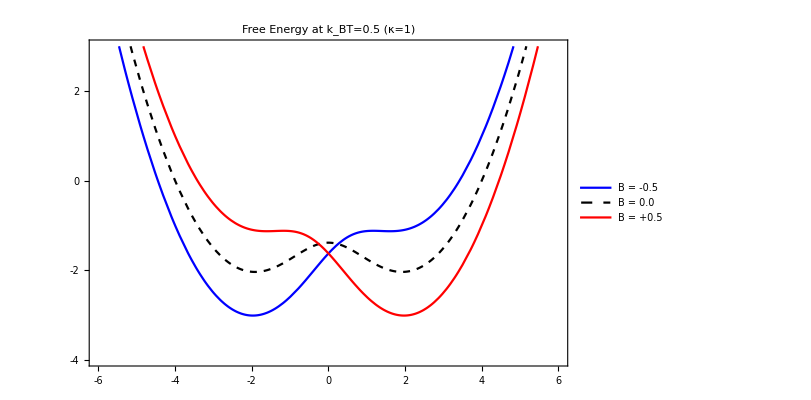

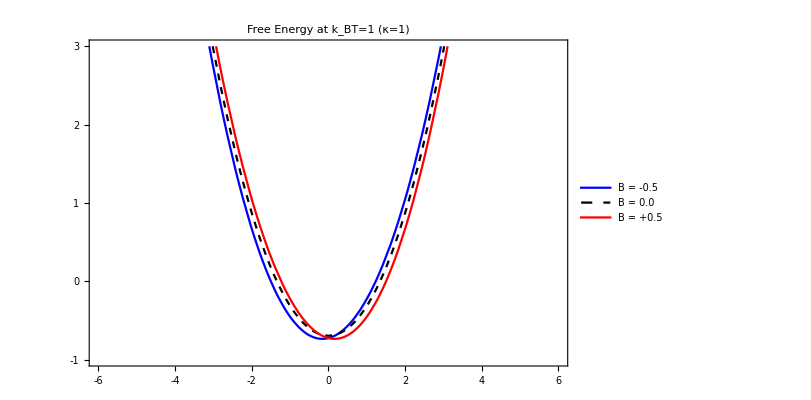

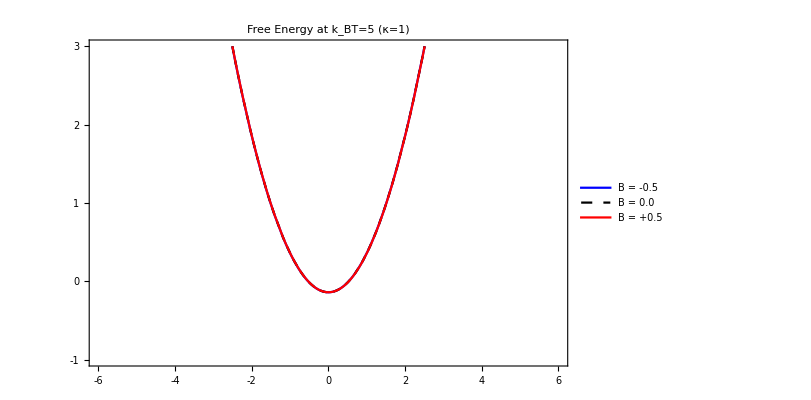

```mathematica
Plot[Evaluate[{f[m,-0.5,1,0.5],f[m,0,1,0.5],f[m,0.5,1,0.5]}],{m,-20,20},PlotLabel->Style["Free Energy at k_BT=0.5 (κ=1)",Black,28],PlotRange->{{-6,6},{-4,3}},PlotLegends->Placed[{Style["B = -0.5",20],Style["B =  0.0",20],Style["B = +0.5",20],Style["B=+±0.0",20],Style["B=+0.1",20],Style["B=+0.2",20]},{0.65,0.75}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {600,400},AspectRatio->Full,PlotStyle->{{Blue},{Black,Dashed},{Red},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2d(5)_image.png",%,ImageResolution->500];Plot[Evaluate[{f[m,-0.5,1,1],f[m,0,1,1],f[m,0.5,1,1]}],{m,-20,20},PlotLabel->Style["Free Energy at k_BT=1 (κ=1)",Black,28],PlotRange->{{-6,6},{-1,3}},PlotLegends->Placed[{Style["B = -0.5",20],Style["B =  0.0",20],Style["B = +0.5",20],Style["B=+±0.0",20],Style["B=+0.1",20],Style["B=+0.2",20]},{0.85,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {600,400},AspectRatio->Full,PlotStyle->{{Blue},{Black,Dashed},{Red},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2d(6)_image.png",%,ImageResolution->500];Plot[Evaluate[{f[m,-0.5,1,5],f[m,0,1,5],f[m,0.5,1,5]}],{m,-20,20},PlotLabel->Style["Free Energy at k_BT=5 (κ=1)",Black,28],PlotRange->{{-6,6},{-1,3}},PlotLegends->Placed[{Style["B = -0.5",20],Style["B =  0.0",20],Style["B = +0.5",20],Style["B=+±0.0",20],Style["B=+0.1",20],Style["B=+0.2",20]},{0.85,0.5}], Frame->{{True,False},{True,False}},FrameLabel->{{Style["",Black,28],None},{Style["",Black,28], None}}, FrameTicks->All,FrameTicksStyle->Directive[Gray,14],ImageSize-> {600,400},AspectRatio->Full,PlotStyle->{{Blue},{Black,Dashed},{Red},{Cyan},{Blue},{Purple},{Black}}]
Export["C:\\Users\\Sina\\Google Drive\\Classes\\Spring 2021\\Statistical Mechanics\\HW6_p2d(7)_image.png",%,ImageResolution->500];
```

```mathematica
Series[Tanh[y(1+x)],{x,0,4}]
```

Tanh[y]+(y-y Tanh[y]^2) x+(-y^2 Tanh[y]+y^2 Tanh[y]^3) x^2+1/3 (-y^3+4 y^3 Tanh[y]^2-3 y^3 Tanh[y]^4) x^3+1/3 (2 y^4 Tanh[y]-5 y^4 Tanh[y]^3+3 y^4 Tanh[y]^5) x^4+O[x]^5

```mathematica
Series[Log[2 Cosh[α/2 (B +κ m)]],{m,0,4}]
```

(Log[2]+Log[Cosh[(B α)/2]])+1/2 α κ Tanh[(B α)/2] m+1/8 (α^2 κ^2-α^2 κ^2 Tanh[(B α)/2]^2) m^2+1/24 (-α^3 κ^3 Tanh[(B α)/2]+α^3 κ^3 Tanh[(B α)/2]^3) m^3+1/192 (-α^4 κ^4+4 α^4 κ^4 Tanh[(B α)/2]^2-3 α^4 κ^4 Tanh[(B α)/2]^4) m^4+O[m]^5

```mathematica
FullSimplify[m-μ/2*Series[Tanh[μ β/2 (κ m +B)],{m,0,3}]/.{κ->J0/μ^2}]
```

-1/2 μ Tanh[(B β μ)/2]+(1-1/4 J0 β Sech[(B β μ)/2]^2) m+(J0^2 β^2 Csch[B β μ]^3 Sinh[(B β μ)/2]^4 m^2)/μ-((J0^3 β^3 (-2+Cosh[B β μ]) Sech[(B β μ)/2]^4) m^3)/(48 μ^2)+O[m]^4

```mathematica
Collect[FullSimplify[m-μ/2(x-x^3/3)/.x->μ β(κ m +B)/2],m]/.κ->(J0/μ^2)
```

1/16 B J0^2 m^2 β^3+(J0^3 m^3 β^3)/(48 μ^2)-1/4 B β μ^2+1/48 B^3 β^3 μ^4+m (1-(J0 β)/4+1/16 B^2 J0 β^3 μ^2)

```mathematica
Series[Log[2Cosh[x]],{x,0,4}]
```

Log[2]+x^2/2-x^4/12+O[x]^5

```mathematica
Collect[FullSimplify[κ/2 m^2-1/β(Log[2]+x^2/2-x^4/12)/.x->μ β(B+κ m)/2]/.κ->J0/μ^2,m]
```

m^2 (1/32 B^2 J0^2 β^3+J0/(2 μ^2)-(J0^2 β)/(8 μ^2))+(J0^4 m^4 β^3)/(192 μ^4)+(B J0^3 m^3 β^3)/(48 μ^2)-1/8 B^2 β μ^2+1/192 B^4 β^3 μ^4+m (-1/4 B J0 β+1/48 B^3 J0 β^3 μ^2)-Log[2]/β

```mathematica
4^3/48
```

4/3

```mathematica
Series[Sqrt[1-x],{x,0,3}]
```

1-x/2-x^2/8-x^3/16+O[x]^4

```mathematica
48/4^3
```

3/4

```mathematica
f[m_,B_,κ_,kBT_]=κ m^2/2-1/kBT Log[2 Cosh[(κ m + B)/(2 kBT)]];
FullSimplify[Series[f[m,0,κ,kBT],{m,0,4}]/κ]/.κ->J0/μ^2
f2=m^2(1-J0 β)/2+b/4 m^4
D[f2,m]
FullSimplify[Solve[%==0,m]/.{J0->4 kB Tc,β->1/(kB T)}]
```

-(μ^2 Log[2])/(J0 kBT)+(1/2-J0/(8 kBT^3 μ^2)) m^2+(J0^3 m^4)/(192 kBT^5 μ^6)+O[m]^5

(b m^4)/4+1/2 m^2 (1-J0 β)

b m^3+m (1-J0 β)

{{m→0},{m→-(√(-1+(4 Tc)/T))/(√b)},{m→(√(-1+(4 Tc)/T))/(√b)}}

```mathematica
Solve[(Collect[m-μ/2(μ β (J0 m/μ^2)/2-(μ β (J0 m/μ^2)/2)^3/3),m]/.{J0->(4 kB Tc),β->1/(kB T)})==0,m]
```

{{m→0},{m→-(ⅈ √3 T √(T-Tc) μ)/(2 Tc^(3/2))},{m→(ⅈ √3 T √(T-Tc) μ)/(2 Tc^(3/2))}}

```mathematica
FullSimplify[Solve[x(-μ/2+m^2/(2μ))+4/3 m^3/μ^2==0,m]/.x->μ B β/2]
```

{{m→1/16 ((384 B β μ^4-B^3 β^3 μ^6+16 √3 √(B^2 β^2 μ^8 (192-B^2 β^2 μ^2)))^(1/3)+B β μ^2 (-1+(B β μ^2)/((384 B β μ^4-B^3 β^3 μ^6+16 √3 √(B^2 β^2 μ^8 (192-B^2 β^2 μ^2)))^(1/3))))},{m→1/32 (-2 B β μ^2+((-1-ⅈ √3) B^2 β^2 μ^4)/((384 B β μ^4-B^3 β^3 μ^6+16 √3 √(B^2 β^2 μ^8 (192-B^2 β^2 μ^2)))^(1/3))+ⅈ (ⅈ+√3) (384 B β μ^4-B^3 β^3 μ^6+16 √3 √(B^2 β^2 μ^8 (192-B^2 β^2 μ^2)))^(1/3))},{m→1/32 (-2 B β μ^2+(ⅈ (ⅈ+√3) B^2 β^2 μ^4)/((384 B β μ^4-B^3 β^3 μ^6+16 √3 √(B^2 β^2 μ^8 (192-B^2 β^2 μ^2)))^(1/3))+(-1-ⅈ √3) (384 B β μ^4-B^3 β^3 μ^6+16 √3 √(B^2 β^2 μ^8 (192-B^2 β^2 μ^2)))^(1/3))}}

```mathematica
Series[Cosh[x],{x,0,4}]
```

1+x^2/2+x^4/24+O[x]^5

```mathematica
Collect[Expand[(x^2+δx^2-2 x δx Cos[θ])^2],δx]
```

x^4+δx^4-4 x^3 δx Cos[θ]-4 x δx^3 Cos[θ]+δx^2 (2 x^2+4 x^2 Cos[θ]^2)

```mathematica
f=tx mx^2/2+ty my^2/2 + ux mx^4/4+ uy my^4/4 +uxy mx^2 my^2/2
FullSimplify[Solve[{D[f,mx]==0,D[f,my]==0},{mx,my},Reals],Assumptions->{tx<0,ty>0,ux>0,uy>0,uxy>0,uxy^2>ux uy}]
FullSimplify[f/.%]
```

(mx^2 tx)/2+(my^2 ty)/2+(mx^4 ux)/4+1/2 mx^2 my^2 uxy+(my^4 uy)/4

{{mx→Undefined,my→Undefined},{mx→Undefined,my→Undefined},{mx→0,my→0},{mx→-√(-tx/ux),my→0},{mx→√(-tx/ux),my→0},{mx→Undefined,my→Undefined},{mx→Undefined,my→Undefined},{mx→Undefined,my→Undefined},{mx→Undefined,my→Undefined}}

{Undefined,Undefined,0,-tx^2/(4 ux),-tx^2/(4 ux),Undefined,Undefined,Undefined,Undefined}

```mathematica
tx=5;ty=10;
ux=1;uy=2;
uxy=10;
Plot3D[f,{mx,-3,3},{my,-3,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
tx=-5;ty=10;
ux=1;uy=2;
uxy=10;
Plot3D[f,{mx,-4,4},{my,-3,3},AxesLabel->Automatic,PlotRange->{-20,100}]
```

-Graphics3D-

```mathematica
tx=5;ty=-10;
ux=1;uy=2;
uxy=10;
Plot3D[f,{mx,-3,3},{my,-3,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
tx=-5;ty=-10;
ux=1;uy=2;
uxy=10;
Plot3D[f,{mx,-3,3},{my,-3,3},AxesLabel->Automatic,PlotRange->{-20,75}]
```

-Graphics3D-

```mathematica
{f/.{mx-> -Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],my-> -Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]},-Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],-Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]}
```

{-12.9032,-0.803219,-2.19971}

```mathematica
Graphics3D[{{Red,PointSize[0.1],Point[{f/.{mx-> Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],my-> Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]},Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]}]},{Red,PointSize[0.1],Point[{f/.{mx-> -Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],my-> Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]},-Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]}]},{Red,PointSize[0.1],Point[{f/.{mx-> Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],my-> -Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]},Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],-Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]}]},{Red,PointSize[0.1],Point[{f/.{mx-> -Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],my-> -Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]},-Sqrt[(uxy ty-uy tx)/(ux uy - uxy^2)],-Sqrt[(uxy tx-ux ty)/(ux uy - uxy^2)]}]}}]
```

-Graphics3D-